```mathematica
star={Quantity[160,  "°"],Quantity[2,  "°"]};
```

```mathematica
moon={Quantity[162,  "°"],Quantity[-4,  "°"]};
```

```mathematica
moon-star
```

{1 35,-7 -3}

```mathematica
Round@JulianDate@DateObject[{-800}, CalendarType -> "Julian"]
```

1429232

```mathematica
Round@JulianDate@DateObject[{200}, CalendarType -> "Julian"]
```

1794109

```mathematica
1000*365*5
```

1825000

MAKE THE FUNCTIONS TO CALL SKYFIELD FROM WL

```mathematica
ExternalFunction
```

```mathematica
session=StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
DeleteObject[session]
```

```mathematica
SetDirectory["~/Desktop/ephemerides"]
```

/Users/christopher/Desktop/ephemerides

```mathematica
ExternalEvaluate[session,"
import json
from skyfield.api import Star, load
from skyfield.data import hipparcos

# Load stellar movement data from Hipparcos
with load.open(hipparcos.URL) as f:
    df = hipparcos.load_dataframe(f)

# Load ephemerides from JPL DE422 for planetary movement
planets = load(\"de422.bsp\")
earth = planets[\"earth\"]
ts = load.timescale()
"]
```

```mathematica
timeFromJD=ExternalFunction[session,"lambda d: ts.tai(jd=d)"]
```

ExternalFunction[…]

```mathematica
planetObject=ExternalFunction[session,"lambda id: planets[id]"]
```

ExternalFunction[…]

```mathematica
objectPosition=ExternalFunction[session,"
def object_position(name,day):
	t = ts.tdb(jd=day)
	obj = planets[name]
	astrometric = earth.at(t).observe(obj)
	lat,long,_ = astrometric.ecliptic_latlon(epoch=t)
	return [lat.degrees, long.degrees]
"]
```

ExternalFunction[…]

```mathematica
starPosition=ExternalFunction[session,"
def star_position(hip,day):
	t = ts.tdb(jd=day)
	obj = Star.from_dataframe(df.loc[hip])
	astrometric = earth.at(t).observe(obj)
	lat,long,_ = astrometric.ecliptic_latlon(epoch=t)
	return [lat.degrees, long.degrees]
"]
```

ExternalFunction[…]

```mathematica
ExternalEvaluate[AstronomicalDiaries`AstronomicalPosition`Private`pythonSession,"print(planets)"]
```

SPICE kernel file 'de422.bsp' has 15 segments

JD 625648.50 - JD 2816816.50  (-3000-11-12 through 3000-01-29)

0 -> 1    SOLAR SYSTEM BARYCENTER -> MERCURY BARYCENTER

0 -> 2    SOLAR SYSTEM BARYCENTER -> VENUS BARYCENTER

0 -> 3    SOLAR SYSTEM BARYCENTER -> EARTH BARYCENTER

0 -> 4    SOLAR SYSTEM BARYCENTER -> MARS BARYCENTER

0 -> 5    SOLAR SYSTEM BARYCENTER -> JUPITER BARYCENTER

0 -> 6    SOLAR SYSTEM BARYCENTER -> SATURN BARYCENTER

0 -> 7    SOLAR SYSTEM BARYCENTER -> URANUS BARYCENTER

0 -> 8    SOLAR SYSTEM BARYCENTER -> NEPTUNE BARYCENTER

0 -> 9    SOLAR SYSTEM BARYCENTER -> PLUTO BARYCENTER

0 -> 10   SOLAR SYSTEM BARYCENTER -> SUN

3 -> 301  EARTH BARYCENTER -> MOON

3 -> 399  EARTH BARYCENTER -> EARTH

1 -> 199  MERCURY BARYCENTER -> MERCURY

2 -> 299  VENUS BARYCENTER -> VENUS

4 -> 499  MARS BARYCENTER -> MARS

```mathematica
j=planetObject["jupiter barycenter"]
```

ExternalObject[…]

```mathematica
t=timeFromJD[JulianDate[Now]]
```

ExternalObject[…]

```mathematica
normalStars["GammaVirginis"]["HipparcosNumber"]
```

61941

```mathematica
star2=starPosition[normalStars["GammaVirginis"]["HipparcosNumber"],JulianDate[DateObject[{-112, 4, 21}, CalendarType -> "Julian"]]+10]
```

{2.95,161.131}

```mathematica
moon2=objectPosition["moon",JulianDate[DateObject[{-112, 4, 21}, CalendarType -> "Julian"]]+10]
```

{-4.98636,163.347}

```mathematica
star2-moon2
```

{7.93635,-2.216}

```mathematica
AbsoluteTiming@Table[objectPosition["moon",JulianDate[DateObject[{-111, 4, 21}, CalendarType -> "Julian"]]],{y,-800,200}]
```

```mathematica
Dynamic[y]
```

```mathematica
JulianDate[DateObject[{-112, 4, 21}, CalendarType -> "Julian"]+14]
```

```mathematica
star3=starPosition[normalStars["AlphaScorpii"]["HipparcosNumber"],JulianDate[DateObject[{-112, 4, 21,20,1,1}, CalendarType -> "Julian"]]+13]
```

{-4.29345,220.43}

```mathematica
moon3=objectPosition["moon",JulianDate[DateObject[{-112, 4, 21,20,1,1}, CalendarType -> "Julian"]]+13]
```

{-3.76139,219.65}

```mathematica
star3-moon3
```

{-0.532062,0.780372}

```mathematica
starPosition[normalStars["EtaGeminorum"]["HipparcosNumber"],JulianDate[DateObject[{-112, 4, 21}, CalendarType -> "Julian"]]+18]-
objectPosition["mercury",JulianDate[DateObject[{-112, 4, 21}, CalendarType -> "Julian"]]+18]
```

{-3.38913,-0.743797}

```mathematica
starPosition[normalStars["MuGeminorum"]["HipparcosNumber"],JulianDate[DateObject[{-112, 4, 21}, CalendarType -> "Julian"]]+19]-
objectPosition["mercury",JulianDate[DateObject[{-112, 4, 21}, CalendarType -> "Julian"]]+19]
```

{-3.25998,-0.539895}

```mathematica
starPosition[normalStars["DeltaCapricorni"]["HipparcosNumber"],JulianDate[DateObject[{-112, 4, 21}, CalendarType -> "Julian"]]+19]-
objectPosition["moon",JulianDate[DateObject[{-112, 4, 21}, CalendarType -> "Julian"]]+19]
```

{-4.76747,-1.73684}

```mathematica
LocalObject
```

```mathematica
2+2
```

4

```mathematica
PacletFind
```

```mathematica
a=CreatePacletArchive[FileNameJoin[{ParentDirectory@NotebookDirectory[],"packages","AstronomicalDiaries"}]]
```

/Users/christopher/Dropbox/brown/2019/asyrScience/finalProject/packages/AstronomicalDiaries-1.0.paclet

```mathematica
Quit
```

```mathematica
foo[2]
```

foo[2]

```mathematica
Quit
```

```mathematica
PacletDirectoryLoad[FileNameJoin[{ParentDirectory@NotebookDirectory[],"packages"}]]
```

{/Users/christopher/Dropbox/brown/2019/asyrScience/finalProject/packages}

```mathematica
Quit
```

```mathematica
Needs["AstronomicalDiaries`"]
```

```mathematica
Length@GetNormalStars[]
```

33

```mathematica
??GetNormalStars
```

```mathematica
GetNormalStars[]
```

{η Piscium,Sheratan,Hamal,Alcyone,Aldebaran,Alnath,ξ Tauri,Propus,Tejat,Alhena,Castor,Pollux,η Cancri,θ Cancri,Asellus Borealis,Asellus Australis,ϵ Leonis,Regulus,ρ Leonis,Chort,Alaraph,Porrima,Spica,α 1 Librae,Zubeneshamali,Dschubba,β 2 Scorpii,Antares,θ Ophiuchi,Dabih,Nashira,Deneb Algiedi,π Scorpii}

```mathematica
?GetNormalStars
```

```mathematica
Quit
```

quit

```mathematica
AstronomicalPosition["test",Today]
```

test

```mathematica
GetNormalStars[][[1]]
```

η Piscium

```mathematica
AstronomicalPosition[Entity["PlanetaryMoon","Moon"],Now]
```

{2.67359,121.559}

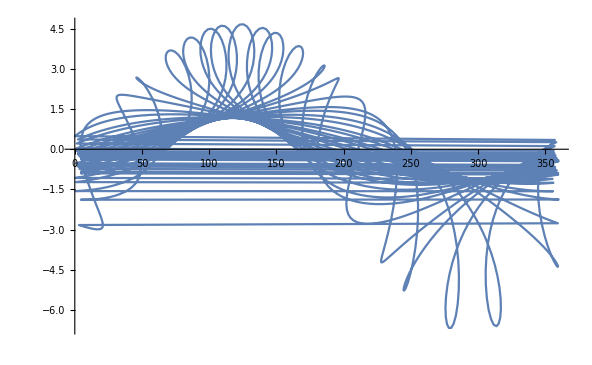

```mathematica
path=AstronomicalPosition[Entity["Planet","Mars"],#]&/@DateRange[DateObject[{-800,1,1}],DateObject[{-760,1,1}],"Week"];
ListLinePlot[path]
```

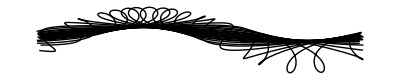

```mathematica
Graphics[Line[Split[path,Abs[#1[[1]]-#2[[1]]]<100&]]]
```

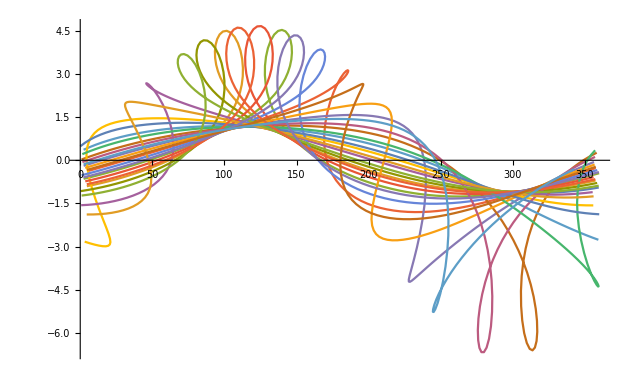

```mathematica
ListLinePlot[Split[path,Abs[#1[[1]]-#2[[1]]]<100&]]
```

```mathematica
Manipulate[ListLinePlot[Split[path,Abs[#1[[1]]-#2[[1]]]<100&],Epilog->{Red,PointSize[Large],Point[path[[n]]]}],{n,1,Length[path],1}]
```

```mathematica
paths=Function[d,AstronomicalPosition[#,d]&/@GetNormalStars[]]/@DateRange[DateObject[{-800}],Today,"Century"];
```

```mathematica
Manipulate[Graphics[Point[paths[[n]]],PlotRange->{{0,360},{-90,90}}],{n,1,Length[paths],1}]
```